```mathematica
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True
```

True

```mathematica
rawData=Import["Desktop/Quant.Trading/round-1-island-data-bottle/prices_round_1_day_-1.csv"];
```

```mathematica
parseString[s_String]:=Module[{clean,data},
clean=StringReplace[s,"_"->""];
data=StringSplit[clean,";"];
data/. ""->0]//ToExpression;

data=(parseString/@(rawData//Flatten))//ToExpression;
```

```mathematica
{Range[Length@data[[1]]],data[[1]]}//Transpose
```

{{1,day},{2,timestamp},{3,product},{4,bidprice1},{5,bidvolume1},{6,bidprice2},{7,bidvolume2},{8,bidprice3},{9,bidvolume3},{10,askprice1},{11,askvolume1},{12,askprice2},{13,askvolume2},{14,askprice3},{15,askvolume3},{16,midprice},{17,profitandloss}}

```mathematica
merc=data[[2;;,3]]//Union
typedData[mercType_,dataType_]:= data[[
Position[data,mercType][[;;,1]],
dataType]];
```

{KELP,RAINFORESTRESIN,SQUIDINK}

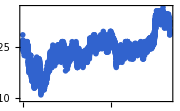
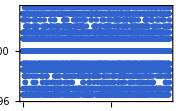
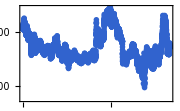

```mathematica
(*mid price distribution*)
Table[
ListPlot[typedData[k,16]//Evaluate,ImageSize->Small],{k,merc}]
```

```mathematica
(*imbalance data*)

(*Simple Aggregate Imbalance*)
mercType=merc[[1]];
bidVolume= typedData[mercType, 5]+ typedData[mercType, 7]+typedData[mercType, 9];
askVolume = typedData[mercType, 11]+ typedData[mercType, 13]+typedData[mercType, 15];

dt = 500;

imb = (bidVolume - askVolume) /(bidVolume + askVolume);

imbData =Table[
{t-dt, imb[[t;;t + dt]]//Mean},{t,1,Length@imb-dt}];
```

```mathematica
(*maybe use price-adjusted imbalance to serve as the moving signal ???*)
```

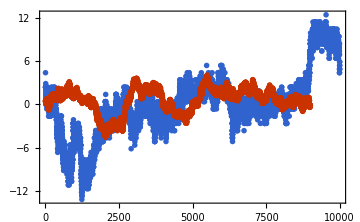

```mathematica
renormalizeData = typedData[mercType,16] - Mean@typedData[mercType,16];

ListPlot[{renormalizeData ,imbdata * 1000} ,ImageSize->Medium]
```